```mathematica
spring - damper system that takes moving average of sample times.
```

Note. We give the received time values the name ' xin' to avoid confusion with actual system time t. The filter ouptut is called 'x'.

There is noise on the wrap time found in the USB packets. The job here is to filter out the noise

### sample times. Each time is time wrap was reported. grep notifyWrap /var/log/system.log | awk ' // { print $7 "," }'

```mathematica
xin={69321093689865,69321264688662,69321435688520,69321605691179,69321776690817,69321947690937,69322117688799,69322288691798,69322459691727,69322629692333,69322800691360,69322971690758,69323141698967,69323312690562,69323483698375,69323653691914,69323824691543,69323995690790,69324165689726,69324336691105,69324507711998,69324677684136,69324848716914,69325019691304,69325189688931,69325360710667,69325531711036,69325701699417,69325872691903,69326043698885,69326213691350,69326384716135,69326555698601,69326726723286,69326896689709,69327067723640,69327238688425,69327408700502,69327579710445,69327750688849,69327920689582,69328091689402,69328262719250,69328432703062,69328603703259,69328774688800,69328944711439,69329115713523,69329286684200,69329456688674,69329627684619,69329798705104,69329968720124,69330139725734,69330310730397,69330480709267,69330651703165,69330822712773,69330992704477,69331163688248,69331334726169,69331504722657,69331675683745,69331846726668,69332016723779,69332187684200,69332358728544,69332528688927,69332699688705,69332870712484,69333040702989,69333211689806,69333382689655,69333552724753,69333723722978,69333894700150,69334064725274,69334235703116,69334406702924,69334576713131,69334747688244,69334918688987,69335088697192,69335259720284,69335430688561,69335600713258,69335771711353,69335942691586,69336112711788,69336283688143,69336454701881,69336624708193,69336795709000,69336966705472,69337136702671,69337307709604,69337478688418,69337649717811,69337819723936,69337990688420,69338161725908,69338331721475,69338502726359,69338673723582,69338843689127,69339014726470,69339185688556,69339355725237,69339526703161,69339697704309,69339867720567,69340038688898,69340209688444,69340379725621,69340550713128,69340721688332,69340891688754,69341062720704,69341233688233,69341403726441,69341574688450,69341745706087,69341915715311,69342086688990,69342257684139,69342427720382,69342598691467,69342769688402,69342939704962,69343110686530,69343281688205,69343451688302,69343622706523,69343793724073,69343963688957,69344134702941,69344305713542,69344475688840,69344646713426,69344817689956,69344987706605,69345158707316,69345329722817,69345499688968,69345670688769,69345841688726,69346011723380,69346182689096,69346353684167,69346523684138,69346694688457,69346865688937,69347035688788,69347206712517,69347377704418,69347548688413,69347718710972,69347889728443,69348060702838,69348230706603,69348401711335,69348572701422,69348742717166,69348913728644,69349084701741,69349254725417,69349425719997,69349596726696,69349766706436,69349937726434,69350108684277,69350278688867,69350449685667,69350620727997,69350790726760,69350961688549,69351132713772,69351302688334,69351473688741,69351644689377,69351814708589,69351985724156,69352156691814,69352326707069,69352497683491,69352668708385,69352838707603,69353009688277,69353180700115,69353350724909,69353521702890,69353692688536,69353862707560,69354033689137,69354204712470,69354374686821,69354545721072,69354716709576,69354886705390,69355057686959,69355228725718,69355398697172,69355569688550,69355740710511,69355910712070,69356081688225,69356252689263,69356422699561,69356593698626,69356764688560,69356934688677,69357105688582,69357276688736,69357447688447,69357617728640,69357788688551,69357959698540,69358129713086,69358300724676,69358471702837,69358641706914,69358812724854,69358983688231,69359153688640,69359324724305,69359495688847,69359665691686,69359836724270,69360007691129,69360177718273,69360348689299,69360519688831,69360689689005,69360860727038,69361031712430,69361201703131,69361372689474,69361543723004,69361713688534,69361884722679,69362055688475,69362225702931,69362396713067,69362567712586,69362737689078,69362908688649,69363079725021,69363249724481,69363420724927,69363591689356,69363761726255,69363932702555,69364103707214,69364273688524,69364444712460,69364615684513,69364785688881,69364956688309,69365127691715,69365297706659,69365468689343,69365639688749,69365809723345,69365980688766,69366151712390,69366321690704,69366492720864,69366663688978,69366833685736,69367004688683,69367175691533,69367346720598,69367516730823,69367687725781,69367858689786,69368028691234,69368199688736,69368370710597,69368540722582,69368711703035,69368882707495,69369052712472,69369223703089,69369394710370,69369564689253,69369735688789,69369906684830,69370076724715,69370247696977,69370418715577,69370588712206,69370759712622,69370930688465,69371100688493,69371271728052,69371442712375,69371612700458,69371783712102,69371954725270,69372124688806,69372295726628,69372466688500,69372636688901,69372807697470,69372978688537,69373148718634,69373319724733,69373490689418,69373660710113,69373831717790,69374002702271,69374172688444,69374343725392,69374514724109,69374684725801,69374855688214,69375026710720,69375196690282,69375367686814,69375538688459,69375708688880,69375879711208,69376050721480,69376220702982,69376391721989,69376562710725,69376733688681,69376903736233,69377074694724,69377245688444,69377415711966,69377586717550,69377757689166,69377927725368,69378098772974,69378269698900,69378439719645,69378610773225,69378781688765,69378951686607,69379122689018,69379293718728,69379463692605,69379634725694,69379805688977,69379975719144,69380146688154,69380317706853,69380487706068,69380658684110,69380829725486,69380999688447,69381170706308,69381341688713,69381511688768,69381682690493,69381853713129,69382023688835,69382194724163,69382365723946,69382535688756,69382706722371,69382877710295,69383047719925,69383218705277,69383389715008,69383559713290,69383730713114,69383901711766,69384071724913,69384242707071,69384413714475,69384583724591,69384754688502,69384925724959,69385095713080,69385266707392,69385437708809,69385607688582,69385778723491,69385949729174,69386119725101,69386290691432,69386461711303,69386632726104,69386802688195,69386973691249,69387144723385,69387314689517,69387485711973,69387656702984,69387826702873,69387997706747,69388168689222,69388338705540,69388509715670,69388680723945,69388850688752,69389021703330,69389192721820,69389362711970,69389533717379,69389704711888,69389874690644,69390045711988,69390216725423,69390386703015,69390557703036,69390728696620,69390898690400,69391069690396,69391240688835,69391410718821,69391581688646,69391752688847,69391922712498,69392093688907,69392264706759,69392434703181,69392605722708,69392776723757,69392946712180,69393117688525,69393288723606,69393458771209,69393629703009,69393800688412,69393970707185,69394141689151,69394312708390,69394482723432,69394653712435,69394824702910,69394994691912,69395165727642,69395336688937,69395506689410,69395677711906,69395848685593,69396018712926,69396189727994,69396360716991,69396531711171,69396701688706,69396872705808,69397043726635,69397213718900,69397384722705,69397555688219,69397725690761,69397896725889,69398067688541,69398237704486,69398408707823,69398579703127,69398749712007,69398920723826,69399091684279,69399261719583,69399432725832,69399603689011,69399773691567,69399944717589,69400115691761,69400285723365,69400456691635,69400627713520,69400797729376,69400968688239,69401139689174,69401309723493,69401480684177,69401651689029,69401821688593,69401992688691,69402163725324,69402333688919,69402504737053,69402675721835,69402845704381,69403016710491,69403187702209,69403357712349,69403528724651,69403699691264,69403869713110,69404040689114,69404211711710,69404381694290,69404552724869,69404723711568,69404893691446,69405064727493,69405235720735,69405405689648,69405576724445,69405747713344,69405918703288,69406088689272,69406259689990,69406430688212,69406600707162,69406771711777,69406942684317,69407112709962,69407283712598,69407454701868,69407624711469,69407795720779,69407966688437,69408136725738,69408307720270,69408478702442,69408648720802,69408819715826,69408990698592,69409160688644,69409331725625,69409502707196,69409672713448,69409843684354,69410014684502,69410184688310,69410355688742,69410526719584,69410696702716,69410867688450,69411038726169,69411208688624,69411379720158,69411550691190,69411720706105,69411891698581,69412062702363,69412232702484,69412403712940,69412574691924,69412744702401,69412915719990,69413086728462,69413256708456,69413427703322,69413598719084,69413768710785,69413939724165,69414110707996,69414280698839,69414451702951,69414622699681,69414792684955,69414963690239,69415134712579,69415304704553,69415475688569,69415646707165,69415817695282,69415987702850,69416158690635,69416329711112,69416499712280,69416670688639,69416841703017,69417011688878,69417182688306,69417353740472,69417523727176,69417694698599,69417865691497,69418035707344,69418206689411,69418377718916,69418547698477,69418718689058,69418889696992,69419059726960,69419230688600,69419401689684,69419571726745,69419742688668,69419913713567,69420083720186,69420254713616,69420425708048,69420595724700,69420766690797,69420937688699,69421107724067,69421278706151,69421449688568,69421619690539,69421790721588,69421961685293,69422131688802,69422302696062,69422473688790,69422643691623,69422814708071,69422985689241,69423155702688,69423326704417,69423497707442,69423667688852,69423838708379,69424009688807,69424179700222,69424350707616,69424521691207,69424691697582,69424862726463,69425033724445,69425204702904,69425374712704,69425545725336,69425716702121,69425886726282,69426057727509,69426228702920,69426398727291,69426569725126,69426740688919,69426910707553,69427081726364,69427252715817,69427422704183,69427593714396,69427764718391,69427934731655,69428105723327,69428276689141,69428446703099,69428617724354,69428788705428,69428958702835,69429129690835,69429300690812,69429470702716,69429641697073,69429812704271,69429982702051,69430153700344,69430324711972,69430494721894,69430665707537,69430836711625,69431006718515,69431177721064,69431348711959,69431518711889,69431689688796,69431860717771,69432030707273,69432201688668,69432372711124,69432542691504,69432713697337,69432884689375,69433054688593,69433225688609,69433396720860,69433566707282,69433737691290,69433908700128,69434078712448,69434249733004,69434420713349,69434590690037,69434761721928,69434932688806,69435103708074,69435273683965,69435444689387,69435615711846,69435785720659,69435956688609,69436127699010,69436297710522,69436468698758,69436639711683,69436809688729,69436980688638,69437151700571,69437321688682,69437492703067,69437663689966,69437833724570,69438004727571,69438175688376,69438345691652,69438516712404,69438687724636,69438857707482,69439028710920,69439199698739,69439369726879,69439540709998,69439711706069,69439881704565,69440052713482,69440223698155,69440393689145,69440564689278,69440735703172,69440905704920,69441076701376,69441247688745,69441417716463,69441588708015,69441759725403,69441929708626,69442100684902,69442271704484,69442441702742,69442612691915,69442783691588,69442953704334,69443124688295,69443295696869,69443465688383,69443636727292,69443807702758,69443977688783,69444148724591,69444319713795,69444490722981,69444660723597,69444831697385,69445002709348,69445172709944,69445343689102,69445514724486,69445684691635,69445855712377,69446026703012,69446196705728,69446367710261,69446538688906,69446708688632,69446879688480,69447050707688,69447220718087,69447391698082,69447562703996,69447732688893,69447903725461,69448074689246,69448244684717,69448415691041,69448586723509,69448756683760,69448927724700,69449098727014,69449268688540,69449439794186,69449610704333,69449780703311,69449951727911,69450122728880,69450292713081,69450463709103,69450634720479,69450804688407,69450975715064,69451146719972,69451316707057,69451487720988,69451658726335,69451828709735,69451999684319,69452170718036,69452340705753,69452511688532,69452682722540,69452852710823,69453023703126,69453194684460,69453364691883,69453535688659,69453706703034,69453876690684,69454047691390,69454218714567,69454389691844,69454559708279,69454730691865,69454901728090,69455071721240,69455242689931,69455413680906,69455583713887,69455754688713,69455925713034,69456095727141,69456266688798,69456437725983,69456607708015,69456778688784,69456949712022,69457119718983,69457290689111,69457461692061,69457631711957,69457802712011,69457973694544,69458143727953,69458314703130,69458485715136,69458655688770,69458826702582,69458997726290,69459167693800,69459338689192,69459509695778,69459679711580,69459850689108,69460021689871,69460191725066,69460362702866,69460533707693,69460703689042,69460874690163,69461045703693,69461215706023,69461386696906,69461557683903,69461727715763,69461898721887,69462069704043,69462239693084,69462410723752,69462581690305,69462751713926,69462922698552,69463093706573,69463263713494,69463434708135,69463605686684,69463775711397,69463946725396,69464117713611,69464288688607,69464458691454,69464629704084,69464800698785,69464970689166,69465141689421,69465312688482,69465482698826,69465653681722,69465824688657,69465994716547,69466165717182,69466336688624,69466506691353,69466677691928,69466848729180,69467018725058,69467189692157,69467360727694,69467530708489,69467701685783,69467872711645,69468042689307,69468213724258,69468384711167,69468554688690,69468725721668,69468896718910,69469066703745,69469237690498,69469408703030,69469578698597,69469749681661,69469920712434,69470090722554,69470261713503,69470432723470,69470602688546,69470773685410,69470944795555,69471114772697};
```

```mathematica
xin=Drop[xin,-20]; (*end is always a mess *)
```

48 kHz
alternateFrameSize is 592 
inputSize= 592 multFactor= 12
outputSize= 588 multFactor= 12
new bufferSize = 98304 numSamplesInBuffer = 8192

```mathematica
bufsize=8192;
```

```mathematica
rate=48000;
```

#### Expected time between wraps in ns

```mathematica
Texpected=10^9 bufsize /rate//N
```

1.70667×10^8

## CHECK We may want to skip the first frames is this is happening consistently

#### If we start at the wrong moment, where the timing is off from the main pulse, the filter has to adjust to get into the beat. Apparently the first beats are off the main beat. This makes huge difference in max error/drift after fitlering.

```mathematica
xin=Drop[xin,5]; (* test. There seems a hickup in sample 3 *)
```

```mathematica
deltas=10^-6(Drop[xin,1]-Drop[xin,-1]);
```

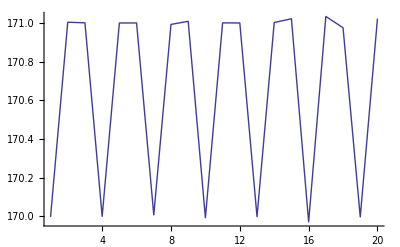

```mathematica
ListPlot[Take[deltas,20],PlotJoined->True,PlotRange->All]
```

```mathematica
(*xin=Take[xin,{200,220}]; (*testing *)
```

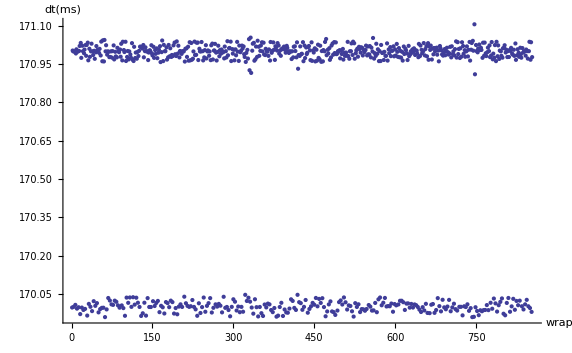

```mathematica
ListPlot[deltas, AxesLabel->{"wrap","dt(ms)"},PlotRange->All]
```

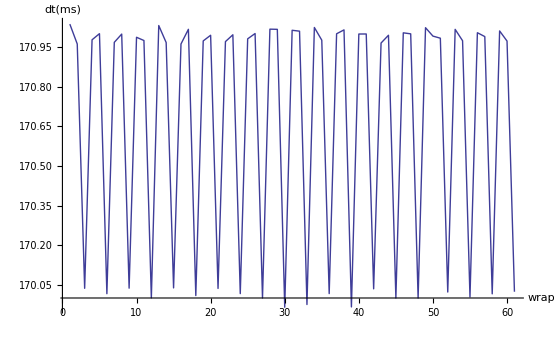

```mathematica
ListPlot[Take[deltas,{100,160}], AxesLabel->{"wrap","dt(ms)"},PlotRange->All,PlotJoined->True]
```

```mathematica
estimated=Mean[10^-6(Drop[xin,1]-Drop[xin,-1])]//N
```

170.672

Is it close?

```mathematica
(Texpected-10^6 estimated)/Texpected
```

-0.0000319831

#### Init the filter with first sample

```mathematica
x0=xin[[1]]
```

69321947690937

```mathematica
xin=Drop[xin,1]; (* first element was used so do not reuse *)
```

```mathematica
x=x0; (* filtered x *)
u=0; (* u = x-xin : the 'error' is the spring extension *)
dx=Texpected; (* dx/dt = expected change rate of filtered x *)
```

```mathematica
xin[[1]]-x
```

169997862

#### Spring constant

```mathematica
K=1;
```

Damping constant

The mass, this determines how slow system follows changes in xin. Bigger=slower.

```mathematica
M=10000;
```

```mathematica
Da=2 √(M K); (*cricital damping *)
```

## Filter

```mathematica
filter[inputx_]:=Module[{},
xnext=x+dx;
du=inputx-x;
dx=(99dx+du)/100; (*exponential towards target *)
x=xnext;
x
]
```

#### spring - damper based filter. Is jumpy.

```mathematica
filter[inputx_]:=Module[{},(*{F,du,xnext,unext},*)
xnext=x+dx ;(* the next filtered output *)
unext=inputx-xnext; (*error u *)

du = unext-u; (* change of the error, for damping *)
F=K unext + Da du; (* force on spring *)
dx = dx + F/M ; 

x=xnext; u=unext; (* update the filter *)
x
];
```

#### spring - damper filter with outlier check/skip

Works great for the test set. Only worry is that the jitter detect uses the du which is change of error.
  An absolute distance of unext from Texpected might be better but in practice it seems worse

```mathematica
filter[inputx_]:=Module[{xnext, unext, du, F},(*{F,du,xnext,unext},*)
xnext=x+dx ;(* the next filtered output *)
unext=inputx-xnext; (*error u *)

du = unext-u; (* change of the error, for damping *)
F=K unext + Da du; (* force on spring *)
dx = dx + F/M ;
x=xnext; u=unext; (* update the filter *)
x
];
```

```mathematica
xfiltered = filter/@xin;
```

```mathematica
10^-6(xfiltered-xin)[[4]]
```

0.645666

### Does it follow xin?

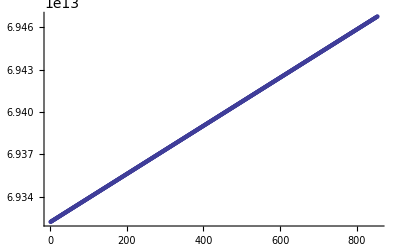

```mathematica
ListPlot[xfiltered]
```

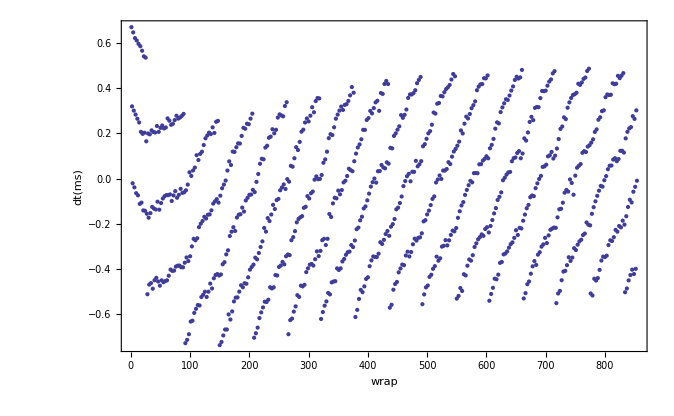

```mathematica
ListPlot[10^-6(xfiltered-xin), FrameLabel->{"wrap","dt(ms)"},PlotRange->All,Frame->True]
```

So the data can come in up to 6 ms late. This is the timestamps straight coming from USB

### Does it keep a solid rate without jumping?

```mathematica
deltas=(Drop[xfiltered,1]-Drop[xfiltered,-1])-Texpected;
```

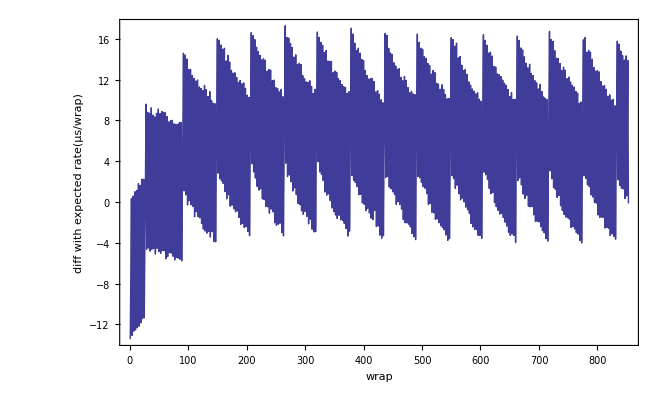

```mathematica
ListPlot[10^-3((Drop[xfiltered,1]-Drop[xfiltered,-1])-Texpected), FrameLabel->{"wrap","diff with expected rate(μs/wrap)"},Frame->True,PlotJoined->True]
```

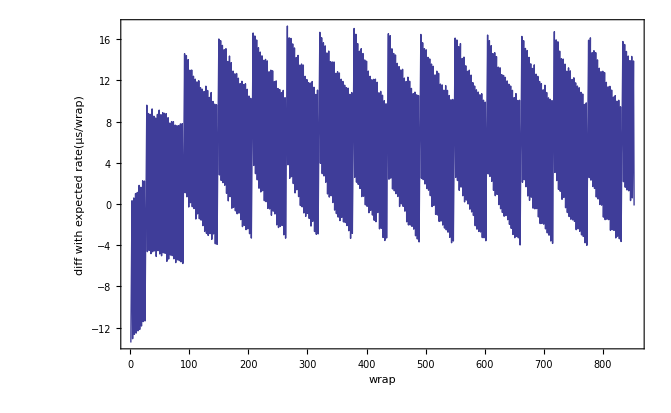

```mathematica
ListPlot[10^-3((Drop[xfiltered,1]-Drop[xfiltered,-1])-Texpected), FrameLabel->{"wrap","diff with expected rate(μs/wrap)"},Frame->True,PlotJoined->True,PlotRange->All]
```